## Three Body Check Hansen & Reid

```mathematica
hansen=Import[FileNameJoin[{NotebookDirectory[],"data","ti-hansen1996.xls"}]];
allTerms=<|1->{"2F"},2->{"3P","3F","3H","1S","1D","1G","1I"},3->{"4S","4D","4F","4G","4I","2P","2D1","2D2","2F1","2F2","2G1","2G2","2H1","2H2","2I","2K","2L"},4->{"5S","5D","5F","5G","5I","3P1","3P2","3P3","3D1","3D2","3F1","3F2","3F3","3F4","3G1","3G2","3G3","3H1","3H2","3H3","3H4","3I1","3I2","3K1","3K2","3L","3M","1S1","1S2","1D1","1D2","1D3","1D4","1F","1G1","1G2","1G3","1G4","1H1","1H2","1I1","1I2","1I3","1K","1L1","1L2","1N"},5->{"6P","6F","6H","4S","4P1","4P2","4D1","4D2","4D3","4F1","4F2","4F3","4F4","4G1","4G2","4G3","4G4","4H1","4H2","4H3","4I1","4I2","4I3","4K1","4K2","4L","4M","2P1","2P2","2P3","2P4","2D1","2D2","2D3","2D4","2D5","2F1","2F2","2F3","2F4","2F5","2F6","2F7","2G1","2G2","2G3","2G4","2G5","2G6","2H1","2H2","2H3","2H4","2H5","2H6","2H7","2I1","2I2","2I3","2I4","2I5","2K1","2K2","2K3","2K4","2K5","2L1","2L2","2L3","2M1","2M2","2N","2O"},6->{"7F","5S","5P","5D1","5D2","5D3","5F1","5F2","5G1","5G2","5G3","5H1","5H2","5I1","5I2","5K","5L","3P1","3P2","3P3","3P4","3P5","3P6","3D1","3D2","3D3","3D4","3D5","3F1","3F2","3F3","3F4","3F5","3F6","3F7","3F8","3F9","3G1","3G2","3G3","3G4","3G5","3G6","3G7","3H1","3H2","3H3","3H4","3H5","3H6","3H7","3H8","3H9","3I1","3I2","3I3","3I4","3I5","3I6","3K1","3K2","3K3","3K4","3K5","3K6","3L1","3L2","3L3","3M1","3M2","3M3","3N","3O","1S1","1S2","1S3","1S4","1P","1D1","1D2","1D3","1D4","1D5","1D6","1F1","1F2","1F3","1F4","1G1","1G2","1G3","1G4","1G5","1G6","1G7","1G8","1H1","1H2","1H3","1H4","1I1","1I2","1I3","1I4","1I5","1I6","1I7","1K1","1K2","1K3","1L1","1L2","1L3","1L4","1M1","1M2","1N1","1N2","1Q"},7->{"8S","6P","6D","6F","6G","6H","6I","4S1","4S2","4P1","4P2","4D1","4D2","4D3","4D4","4D5","4D6","4F1","4F2","4F3","4F4","4F5","4G1","4G2","4G3","4G4","4G5","4G6","4G7","4H1","4H2","4H3","4H4","4H5","4I1","4I2","4I3","4I4","4I5","4K1","4K2","4K3","4L1","4L2","4L3","4M","4N","2S1","2S2","2P1","2P2","2P3","2P4","2P5","2D1","2D2","2D3","2D4","2D5","2D6","2D7","2F1","2F2","2F3","2F4","2F5","2F6","2F7","2F8","2F9","2F10","2G1","2G2","2G3","2G4","2G5","2G6","2G7","2G8","2G9","2G10","2H1","2H2","2H3","2H4","2H5","2H6","2H7","2H8","2H9","2I1","2I2","2I3","2I4","2I5","2I6","2I7","2I8","2I9","2K1","2K2","2K3","2K4","2K5","2K6","2K7","2L1","2L2","2L3","2L4","2L5","2M1","2M2","2M3","2M4","2N1","2N2","2O","2Q"},8->{"7F","5S","5P","5D1","5D2","5D3","5F1","5F2","5G1","5G2","5G3","5H1","5H2","5I1","5I2","5K","5L","3P1","3P2","3P3","3P4","3P5","3P6","3D1","3D2","3D3","3D4","3D5","3F1","3F2","3F3","3F4","3F5","3F6","3F7","3F8","3F9","3G1","3G2","3G3","3G4","3G5","3G6","3G7","3H1","3H2","3H3","3H4","3H5","3H6","3H7","3H8","3H9","3I1","3I2","3I3","3I4","3I5","3I6","3K1","3K2","3K3","3K4","3K5","3K6","3L1","3L2","3L3","3M1","3M2","3M3","3N","3O","1S1","1S2","1S3","1S4","1P","1D1","1D2","1D3","1D4","1D5","1D6","1F1","1F2","1F3","1F4","1G1","1G2","1G3","1G4","1G5","1G6","1G7","1G8","1H1","1H2","1H3","1H4","1I1","1I2","1I3","1I4","1I5","1I6","1I7","1K1","1K2","1K3","1L1","1L2","1L3","1L4","1M1","1M2","1N1","1N2","1Q"},9->{"6P","6F","6H","4S","4P1","4P2","4D1","4D2","4D3","4F1","4F2","4F3","4F4","4G1","4G2","4G3","4G4","4H1","4H2","4H3","4I1","4I2","4I3","4K1","4K2","4L","4M","2P1","2P2","2P3","2P4","2D1","2D2","2D3","2D4","2D5","2F1","2F2","2F3","2F4","2F5","2F6","2F7","2G1","2G2","2G3","2G4","2G5","2G6","2H1","2H2","2H3","2H4","2H5","2H6","2H7","2I1","2I2","2I3","2I4","2I5","2K1","2K2","2K3","2K4","2K5","2L1","2L2","2L3","2M1","2M2","2N","2O"},10->{"5S","5D","5F","5G","5I","3P1","3P2","3P3","3D1","3D2","3F1","3F2","3F3","3F4","3G1","3G2","3G3","3H1","3H2","3H3","3H4","3I1","3I2","3K1","3K2","3L","3M","1S1","1S2","1D1","1D2","1D3","1D4","1F","1G1","1G2","1G3","1G4","1H1","1H2","1I1","1I2","1I3","1K","1L1","1L2","1N"},11->{"4S","4D","4F","4G","4I","2P","2D1","2D2","2F1","2F2","2G1","2G2","2H1","2H2","2I","2K","2L"},12->{"3P","3F","3H","1S","1D","1G","1I"},13->{"2F"}|>;
ThreeBodyTable=Import[FileNameJoin[{NotebookDirectory[],"data","ThreeBodyTable.m"}]];
```

```mathematica
Length/@allTerms
```

<|1→1,2→7,3→17,4→47,5→73,6→119,7→119,8→119,9→73,10→47,11→17,12→7,13→1|>

```mathematica
Tops={T2,T3,T4,T6,T7,T8,T11,T12,T14,T15,T16,T17,T18,T19};
hansenA=<||>;
Do[hansenA[Tope]=<||>,{Tope,Tops}];
Do[
(
hansenData=hansen[[index]];
hansenData=hansenData[[2;;]];
Do[(
Tope=Tops[[Tindex]];
hansenRow=hansenData[[rowIndex]];
hansenKey=Prepend[hansenRow[[;;2]],index+1];
{numE,bterm,kterm}=hansenKey;
hansenValues=hansenRow[[3;;]];
hansenA[Tope][hansenKey] = hansenValues[[Tindex]];
),
{Tindex,1,Length[Tops]},
{rowIndex,1,Length[hansenData]}]
)
,{index,2,6,1}];
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross.m"}];
fncrossReid=Import[fncrossReidfname];
Tsubset={T2,T3,T4,T6,T7,T8};
```

```mathematica
ourmats=<||>;
mikemats=<||>;
hansenmats=<||>;
diffs=Table[(
terms=allTerms[numElectrons];
ours=Table[Coefficient[ThreeBodyTable[{numElectrons,braTerm,ketTerm}],Tsubset],{braTerm,terms},{ketTerm,terms}];
mikes=Table[
(
row=fncrossReid["E-S"][#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},
{ketTerm,terms}];
hansens=Table[
(
row=hansenA[#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},{ketTerm,terms}];
hansenmats[numElectrons]=hansens;
ourmats[numElectrons]=ours;
mikemats[numElectrons]=mikes;
mats={ours,mikes,hansens};
tab=Table[
(
mat1=Flatten[N[mats[[i]][[;;,;;,idx]]]];
mat2=Flatten[N[mats[[j]][[;;,;;,idx]]]];
cossim=mat1.mat2/Norm[mat1]/Norm[mat2];
N[cossim,5]),
{idx,1,Length[Tsubset]},
{i,1,3},
{j,1,3}
];
tab
),
{numElectrons,3,7}];
```

```mathematica
MatrixForm[diffs]
```

((1. | 0.886449 | 1.
0.886449 | 1. | 0.886449
1. | 0.886449 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.840415 | 1.
0.840415 | 1. | 0.840415
1. | 0.840415 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.653241 | 1.
0.653241 | 1. | 0.653241
1. | 0.653241 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.496742 | 1.
0.496742 | 1. | 0.496742
1. | 0.496742 | 1.) | (1. | 0.701095 | 1.
0.701095 | 1. | 0.701095
1. | 0.701095 | 1.) | (1. | 0.998195 | 1.
0.998195 | 1. | 0.998195
1. | 0.998195 | 1.) | (1. | 0.622542 | 1.
0.622542 | 1. | 0.622542
1. | 0.622542 | 1.) | (1. | 0.786432 | 1.
0.786432 | 1. | 0.786432
1. | 0.786432 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.543001 | 1.
0.543001 | 1. | 0.543001
1. | 0.543001 | 1.) | (1. | 0.995265 | 1.
0.995265 | 1. | 0.995265
1. | 0.995265 | 1.) | (1. | 0.929128 | 1.
0.929128 | 1. | 0.929128
1. | 0.929128 | 1.) | (1. | 0.975857 | 1.
0.975857 | 1. | 0.975857
1. | 0.975857 | 1.) | (1. | 0.952609 | 1.
0.952609 | 1. | 0.952609
1. | 0.952609 | 1.) | (1. | 0.909192 | 1.
0.909192 | 1. | 0.909192
1. | 0.909192 | 1.))

```mathematica
ArcCos[0.915]/π*180
```

23.7943

```mathematica
Manipulate[(
rowOurs=MatrixPlot/@(ourmats[idx][[;;,;;,#]]&/@Range[1,6]);
rowReid=MatrixPlot/@(mikemats[idx][[;;,;;,#]]&/@Range[1,6]);
rowHansens=MatrixPlot/@(hansenmats[idx][[;;,;;,#]]&/@Range[1,6]);
Grid[{rowOurs,rowReid,rowHansens}]),{idx,3,7,1},
TrackedSymbols:>idx]
```

```mathematica
rowOurs=(ourmats[6][[;;,;;,#]]&/@Range[1,6]);
```

```mathematica
EigenDistance[mat1_,mat_]:=(
eigen1=Eigenvalues[mat1];
eigen2=Eigenvalues[mat2];
eigen1=Sort[Re[eigen1]];
eigen2=Sort[Re[eigen2]];
Return[(eigen1.eigen2)/(Norm[eigen1]Norm[eigen2])]
)
ourmats=<||>;
mikemats=<||>;
hansenmats=<||>;
diffs=Table[(
terms=allTerms[numElectrons];
ours=Table[Coefficient[ThreeBodyTable[{numElectrons,braTerm,ketTerm}],Tsubset],{braTerm,terms},{ketTerm,terms}];
mikes=Table[
(
row=fncrossReid["E-S"][#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},
{ketTerm,terms}];
hansens=Table[
(
row=hansenA[#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},{ketTerm,terms}];
hansenmats[numElectrons]=hansens;
ourmats[numElectrons]=ours;
mikemats[numElectrons]=mikes;
mats={ours,mikes,hansens};
tab=Table[
(
mat1=N[mats[[i]][[;;,;;,idx]]];
mat2=N[mats[[j]][[;;,;;,idx]]];
cossim=EigenDistance[mat1,mat2];
N[cossim,5]),
{idx,1,Length[Tsubset]},
{i,1,3},
{j,1,3}
];
tab
),
{numElectrons,3,7}];
```

```mathematica
MatrixForm[diffs]
```

((1. | 0.942488 | 1.
0.942488 | 1. | 0.942488
1. | 0.942488 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.950198 | 1.
0.950198 | 1. | 0.950198
1. | 0.950198 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.941184 | 1.
0.941184 | 1. | 0.941184
1. | 0.941184 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.962546 | 1.
0.962546 | 1. | 0.962546
1. | 0.962546 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 0.999878 | 1.
0.999878 | 1. | 0.999878
1. | 0.999878 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
(1. | 0.955945 | 1.
0.955945 | 1. | 0.955945
1. | 0.955945 | 1.) | (1. | 0.99807 | 1.
0.99807 | 1. | 0.99807
1. | 0.99807 | 1.) | (1. | 0.995833 | 1.
0.995833 | 1. | 0.995833
1. | 0.995833 | 1.) | (1. | 0.996811 | 1.
0.996811 | 1. | 0.996811
1. | 0.996811 | 1.) | (1. | 0.997851 | 1.
0.997851 | 1. | 0.997851
1. | 0.997851 | 1.) | (1. | 0.99517 | 1.
0.99517 | 1. | 0.99517
1. | 0.99517 | 1.))

## Michael Reid' s Data from Crosswhite

```mathematica
Protect/@{M0,M2,M4,P2,P4,P6,F2,F4,F6,α,β,γ};
```

```mathematica
RemoveWhiteSpace[str_]:=(
Return[StringReplace[str,RegularExpression["\\s+"]->" "]];
);

RemoveAllWhite[str_]:=(
Return[StringReplace[str,RegularExpression["\\s"]->""]]
);

ParseCFPRow[row_]:=(
numChunks=Round[StringLength[row]/16];
pieces=Table[StringTake[row,{16*i+1,16*(i+1)}],{i,0,numChunks-1,1}];
Return[pieces]
);

ParseCFPRows[rows_]:=ParseCFPAtom/@Flatten[ParseCFPRow/@rows];
ParseCFPAtom[atom_]:={ToExpression[StringTake[atom,{1,4}]],
ToExpression[StringTake[atom,{5,16}]]};

BraKetRowParser[row_]:=(
bra=RemoveAllWhite[StringTake[row,{2,4}]];
ket=RemoveAllWhite[StringTake[row,{6,8}]];
nums=RemoveWhiteSpace[StringTake[row,{9,-1}]];
nums=ToExpression/@StringSplit[nums," "];
Return[{bra,ket,nums}]
);

SingleTermParser[row_]:=(
term=RemoveAllWhite[StringTake[row,{2,4}]];
nums=StringTake[row,{8,-1}];
nums=RemoveWhiteSpace[nums];
nums=ToExpression/@StringSplit[nums," "];
Return[{term,nums}]
);

OffDiagonalParser[row_]:=(
prow=RemoveWhiteSpace[row];
prow=StringSplit[prow," "];
prow=Partition[prow,2];
prow={
ToExpression[#[[1]]],
ToExpression[StringTake[#[[2]],{1,-7}]],
ToExpression[StringTake[#[[2]],{-6,-4}]],
ToExpression[StringTake[#[[2]],{-3,-1}]]}&/@prow;
Return[prow]
);

ClearAll[CrossWhiteParser];
CrossWhiteParser[maxElectrons_]:=
(cfps=<||>;
fnTerms=<||>;
UK=<||>;
paramSymbols={F2,F4,F6,α,β,γ,T2,T3,T4,T6,T7,T8};
MKPKs=<|
M0-><||>,M2-><||>,M4-><||>,
P2-><||>,P4-><||>,P6-><||>|>;
UKs=<|0-><||>,1-><||>,2-><||>,3-><||>,
4-><||>,5-><||>,6-><||>|>;
V1Ks=<|0-><||>,1-><||>,2-><||>,3-><||>,
4-><||>,5-><||>,6-><||>|>;
ESs=<|F2-><||>,F4-><||>,F6-><||>,
α-><||>,β-><||>,γ-><||>,
T2-><||>,T3-><||>,T4-><||>,T6-><||>,T7-><||>,T8-><||>|>;
Do[
(
PrintTemporary[numElectrons];
EStermTally={};
fnameTemplate=StringTemplate["f`numElectrons`cross"];
crossFile=FileNameJoin[{NotebookDirectory[],"data","fncrosswhite",fnameTemplate[<|"numElectrons"->numElectrons|>]}];
crossData=Import[crossFile,"Text"];
crossData=StringSplit[crossData,"\n"];
(*the first line echoes the configuration and gives then number of terms*)
(*the next following lines enumerates the terms*)
numterms=ToExpression[StringTake[crossData[[1]],{21,24}]];
(*There are at most 20 term string per row*)
numTermRows=Ceiling[numterms/20];
(*Grab those rows.*)
terms=crossData[[2;;2+numTermRows-1]];
terms=RemoveWhiteSpace[terms];
(*Split the resulting string.*)
allterms=Flatten[StringSplit[terms," "]];
fnTerms[numElectrons]=allterms;

crossData=crossData[[2+numTermRows;;]];

cursor=1;
regularOps={"U(K)","V(1K)","MK,PK"};

While[
cursor<=Length[crossData],
(
line=crossData[[cursor]];

If[StringContainsQ[line,"END"],
(*finish table parsing*)
(
cursor+=1;
Continue[]
)
];

If[StringContainsQ[line,"STATES"],
(*start table parsing*)
(
offdiagonal={};
tableHeader=StringSplit[RemoveWhiteSpace[line]," "][[1]];
cursor+=1;
Continue[]
)
];

If[
tableHeader=="CFP",
(
daughter=StringReplace[StringTake[line,{6,9}],RegularExpression["\\s"]->""];
cfpKey={numElectrons,daughter};
parentTerms=If[numElectrons>1,
fnTerms[numElectrons-1],
allterms];
numCFPs=ToExpression[StringTake[line,{9,-1}]];
numRows=Ceiling[numCFPs/5];
startRow=cursor+1;
endRow=cursor+numRows;
dataRows=Take[crossData,{startRow,endRow}];
dataRow=ParseCFPRows[dataRows];
dataRow=Select[dataRow,Length[#]>0&];
dataRow={parentTerms[[#[[1]]]],#[[2]]}&/@dataRow;
dataRow={daughter,dataRow};
dataRow=Flatten[dataRow,1];
cfps[cfpKey]=dataRow;
cursor+=numRows+1;
)
];

If[
MemberQ[regularOps,tableHeader],
(
line=crossData[[cursor]];
parsedRow=BraKetRowParser[line];
If[tableHeader=="MK,PK",
(
{M0v,M2v,M4v,P2v,P4v,P6V}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
MKPKs[M0][{numElectrons,braTerm,keyTerm}]=M0v;
MKPKs[M2][{numElectrons,braTerm,keyTerm}]=M2v;
MKPKs[M4][{numElectrons,braTerm,keyTerm}]=M4v;
MKPKs[P2][{numElectrons,braTerm,keyTerm}]=P2v;
MKPKs[P4][{numElectrons,braTerm,keyTerm}]=P4v;
MKPKs[P6][{numElectrons,braTerm,keyTerm}]=P6V;
)
];

If[tableHeader=="U(K)",
(
{U0v,U1v,U2v,U3v,U4v,U5v,U6v}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
UKs[0][{numElectrons,braTerm,keyTerm}]=U0v;
UKs[1][{numElectrons,braTerm,keyTerm}]=U1v;
UKs[2][{numElectrons,braTerm,keyTerm}]=U2v;
UKs[3][{numElectrons,braTerm,keyTerm}]=U3v;
UKs[4][{numElectrons,braTerm,keyTerm}]=U4v;
UKs[5][{numElectrons,braTerm,keyTerm}]=U5v;
UKs[6][{numElectrons,braTerm,keyTerm}]=U6v;
)
];

If[tableHeader=="V(1K)",
(
{U0v,U1v,U2v,U3v,U4v,U5v,U6v}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
V1Ks[0][{numElectrons,braTerm,keyTerm}]=U0v;
V1Ks[1][{numElectrons,braTerm,keyTerm}]=U1v;
V1Ks[2][{numElectrons,braTerm,keyTerm}]=U2v;
V1Ks[3][{numElectrons,braTerm,keyTerm}]=U3v;
V1Ks[4][{numElectrons,braTerm,keyTerm}]=U4v;
V1Ks[5][{numElectrons,braTerm,keyTerm}]=U5v;
V1Ks[6][{numElectrons,braTerm,keyTerm}]=U6v;
)
];

cursor++;
)
];

If[
And[tableHeader=="E-S",numElectrons==2],
(
line=crossData[[cursor]];
{term,nums}=SingleTermParser[line];
If[
StringMatchQ[term,RegularExpression["[^a-zA-Z]*"]],
(
nums=OffDiagonalParser[line];
Do[
({val,paramIndex,braTermIndex,ketTermIndex}=num;
braTerm=allterms[[braTermIndex]];
ketTerm=allterms[[ketTermIndex]];
paramSymbol=paramSymbols[[paramIndex]];
key={numElectrons,braTerm,ketTerm};
symkey={numElectrons,ketTerm,braTerm};
ESs[paramSymbol][key]=val;
ESs[paramSymbol][symkey]=val;
),
{num,nums}]
),
(
(*save the diagonal terms*)
{F2v,F4v,F6v,αv,βv,γv}=nums;
{braTerm,keyTerm}=parsedRow[[1;;2]];
ESs[F2][{numElectrons,braTerm,keyTerm}]=F2v;
ESs[F4][{numElectrons,braTerm,keyTerm}]=F4v;
ESs[F6][{numElectrons,braTerm,keyTerm}]=F6v;
ESs[α][{numElectrons,braTerm,keyTerm}]=αv;
ESs[β][{numElectrons,braTerm,keyTerm}]=βv;
ESs[γ][{numElectrons,braTerm,keyTerm}]=γv;
)
];
cursor++;
)
];

If[
And[tableHeader=="E-S",numElectrons>2],
(
line=crossData[[cursor]];
{term,nums}=SingleTermParser[line];
If[
StringMatchQ[term,RegularExpression["[^a-zA-Z]*"]],
(
(*the off-diagonal block*)
nums=OffDiagonalParser[line];
Do[
({val,paramIndex,braTermIndex,ketTermIndex}=num;
braTerm=allterms[[braTermIndex]];
ketTerm=allterms[[ketTermIndex]];
paramSymbol=paramSymbols[[paramIndex]];
key={numElectrons,braTerm,ketTerm};
symkey={numElectrons,ketTerm,braTerm};
ESs[paramSymbol][key]=val;
ESs[paramSymbol][symkey]=val;
),
{num,nums}]
),
(
(*the diagonal block*)
If[
!MemberQ[EStermTally,term],
{F2v,F4v,F6v,αv,βv,γv}=nums,
{T2v,T3v,T4v,T6v,T7v,T8v}=nums
];
{braTerm,keyTerm}={term,term};
If[!MemberQ[EStermTally,term],
(
ESs[F2][{numElectrons,braTerm,keyTerm}]=F2v;
ESs[F4][{numElectrons,braTerm,keyTerm}]=F4v;
ESs[F6][{numElectrons,braTerm,keyTerm}]=F6v;
ESs[α][{numElectrons,braTerm,keyTerm}]=αv;
ESs[β][{numElectrons,braTerm,keyTerm}]=βv;
ESs[γ][{numElectrons,braTerm,keyTerm}]=γv;
),
(
(*Print[term," ahoy"];*)
ESs[T2][{numElectrons,braTerm,keyTerm}]=T2v;
ESs[T3][{numElectrons,braTerm,keyTerm}]=T3v;
ESs[T4][{numElectrons,braTerm,keyTerm}]=T4v;
ESs[T6][{numElectrons,braTerm,keyTerm}]=T6v;
ESs[T7][{numElectrons,braTerm,keyTerm}]=T7v;
ESs[T8][{numElectrons,braTerm,keyTerm}]=T8v;
)
];
(*Print[term,"-",EStermTally,MemberQ[EStermTally,term]];*)
EStermTally=Append[EStermTally,term];
)
];
cursor++;
)
];

)
];
tables["terms"]=Flatten[allterms];
),
{numElectrons,1,maxElectrons,1}
];
outPut=<|
"terms"->fnTerms,
"CFP"->cfps,
"MKPK"->MKPKs,
"UK"->UKs,
"V1K"->V1Ks,
"E-S"->ESs
|>;
Return[outPut];
)
```

```mathematica
OffDiagonalParser["  -1.271348  7074075   0.448249  7075076   2.436493  7075077  -0.228128  7079080    "]
```

{{-1.27135,7,74,75},{0.448249,7,75,76},{2.43649,7,75,77},{-0.228128,7,79,80}}

```mathematica
OffDiagonalParser["  -0.043768  1007008  -0.208463  1009010   0.249517  1011012   0.126404  1013014    "]
```

{{-0.043768,1,7,8},{-0.208463,1,9,10},{0.249517,1,11,12},{0.126404,1,13,14}}

```mathematica
fncross=CrossWhiteParser[7];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","fncross.m"}],fncross]
```

/Users/juan/ZiaLab/Codebase/qlanth/data/fncross.m

```mathematica
fncross=Import["/Users/juan/ZiaLab/Codebase/qlanth/data/fncross.m"];
```

```mathematica
Print[Style["hello",Bold]<>"hello"]
```

```mathematica
word1="Hello";
word2="world";

boldString=Row[{word1," ",Style[word2,Bold]}];

Print[boldString]
```

Hello world

```mathematica
word1="Hello";
word2="world";

boldString=StringJoin[word1," ",ToString[Style[word2,Bold]]];

Print[boldString]
```

Hello world

```mathematica
word1="Hello";
word2="world";

boldString=Style[word1<>" "<>Style[word2,Bold],"Text"];

Print[boldString]
```

StringJoin::string: String expected at position 2 in Hello <>world.

Hello <>world

```mathematica
ClearAll[message,symbolName,fname,importantThings]
```

```mathematica
importCommand
```

fncrossReid=Import["/Users/juan/ZiaLab/Codebase/qlanth/data/fncross.m"];

```mathematica
Clear[fncrossReid]
```

```mathematica
ImportData["Reid-fncross"]
```

Importing data for reduced matrix elements from Reid's linuxemp as fncrossReid.

```mathematica
fncrossReid
```

```mathematica
fncrossReid
```

```mathematica
ImportFN[]
```

```mathematica
fncrossWhite
```

```mathematica
fncross//Keys
```

{terms,CFP,MKPK,UK,V1K,E-S}

```mathematica
fncross["E-S"][T2]
```

<|{3,2D1,2D2}→0.135652,{3,2F1,2F2}→0.710705,{3,2G1,2G2}→0.128889,{4,3P1,3P2}→-0.111117,{4,3P1,3P3}→0.167515,{4,3P2,3P3}→-0.15736,{4,3D1,3D2}→-0.405,{4,3F1,3F3}→-0.25951,{4,3F2,3F3}→0.14942,{4,3F3,3F4}→-0.85491,{4,3G1,3G2}→-0.38481,{4,3G1,3G3}→0.47422,{4,3G2,3G3}→0.7321,{4,3H1,3H2}→0.030305,{4,3H1,3H4}→0.31542,{4,3H2,3H4}→-0.2963,{4,3H3,3H4}→0.79352,{4,3I1,3I2}→0.31812,{4,3K1,3K2}→1.00969,{4,1S1,1S2}→2.84282,{4,1D1,1D2}→0.05621,{4,1D1,1D3}→0.42876,{4,1D1,1D4}→0.62616,{4,1D2,1D3}→0.19813,{4,1D2,1D4}→-0.25319,{4,1G1,1G2}→0.02044,{4,1G1,1G3}→0.40738,{4,1G1,1G4}→0.32498,{4,1G2,1G3}→0.18825,{4,1G2,1G4}→-0.1314,{4,1I1,1I2}→-0.03577,{4,1I1,1I3}→0.27872,{4,1I2,1I3}→-0.1127,{5,4P1,4P2}→-0.380716,{5,4D1,4D2}→-0.524977,{5,4D1,4D3}→0.775443,{5,4D2,4D3}→0.239801,{5,4F1,4F3}→1.25636,{5,4F2,4F3}→-0.08847,{5,4F3,4F4}→-1.09001,{5,4G1,4G2}→-0.190901,{5,4G1,4G3}→0.736784,{5,4G1,4G4}→-1.72516,{5,4G2,4G3}→0.227846,{5,4G2,4G4}→0.604629,{5,4G3,4G4}→0.933429,{5,4H1,4H3}→-0.716864,{5,4H2,4H3}→1.01174,{5,4I1,4I2}→0.334076,{5,4I1,4I3}→-1.15728,{5,4I2,4I3}→0.405597,{5,4K1,4K2}→1.28735,{5,2P1,2P2}→-0.107143,{5,2P1,2P3}→0.408627,{5,2P1,2P4}→-0.613885,{5,2P2,2P3}→-0.216707,{5,2P2,2P4}→-0.347266,{5,2P3,2P4}→0.649794,{5,2D1,2D2}→1.06261,{5,2D1,2D3}→-0.274184,{5,2D1,2D4}→-0.229498,{5,2D1,2D5}→0.092916,{5,2D2,2D3}→-0.305217,{5,2D2,2D4}→-0.413843,{5,2D2,2D5}→0.921954,{5,2D3,2D4}→-0.017042,{5,2D3,2D5}→0.092916,{5,2D4,2D5}→0.229211,{5,2F1,2F2}→-1.79796,{5,2F1,2F4}→-0.271052,{5,2F1,2F6}→0.857143,{5,2F2,2F3}→0.112604,{5,2F2,2F4}→-0.049839,{5,2F2,2F5}→-0.306034,{5,2F2,2F6}→-0.348045,{5,2F2,2F7}→-0.530067,{5,2F3,2F4}→0.127004,{5,2F3,2F6}→0.254492,{5,2F4,2F5}→0.775775,{5,2F4,2F6}→-0.090419,{5,2F4,2F7}→-0.108521,{5,2F5,2F6}→-0.337182,{5,2F5,2F7}→0.186893,{5,2F6,2F7}→-1.04324,{5,2G1,2G2}→1.00963,{5,2G1,2G3}→-0.099703,{5,2G1,2G4}→-0.218056,{5,2G1,2G5}→-0.930654,{5,2G1,2G6}→0.169641,{5,2G2,2G3}→-0.29,{5,2G2,2G4}→-0.013053,{5,2G2,2G5}→0.262072,{5,2G2,2G6}→-0.263534,{5,2G3,2G4}→-0.016192,{5,2G3,2G5}→0.586845,{5,2G3,2G6}→0.169641,{5,2G4,2G5}→-0.664334,{5,2G4,2G6}→-0.006443,{5,2G5,2G6}→0.197105,{5,2H1,2H3}→0.029221,{5,2H1,2H5}→0.769419,{5,2H1,2H6}→-0.311559,{5,2H1,2H7}→-0.296535,{5,2H2,2H4}→-0.367563,{5,2H2,2H5}→0.284058,{5,2H2,2H6}→-0.848614,{5,2H2,2H7}→-0.029699,{5,2H3,2H5}→-0.408046,{5,2H3,2H6}→-0.176244,{5,2H3,2H7}→-0.167745,{5,2H4,2H5}→-0.720068,{5,2H4,2H6}→-0.114061,{5,2H4,2H7}→-0.068779,{5,2H5,2H6}→-0.277774,{5,2H5,2H7}→0.409745,{5,2H6,2H7}→-0.552978,{5,2I1,2I2}→0.174481,{5,2I1,2I3}→-0.624302,{5,2I1,2I4}→-0.048212,{5,2I1,2I5}→-0.281121,{5,2I2,2I3}→0.393668,{5,2I2,2I4}→-0.048212,{5,2I2,2I5}→-0.281121,{5,2I3,2I4}→0.713772,{5,2I3,2I5}→0.162305,{5,2I4,2I5}→0.457825,{5,2K1,2K2}→0.064376,{5,2K1,2K3}→0.361441,{5,2K1,2K4}→-1.20694,{5,2K1,2K5}→0.017412,{5,2K2,2K3}→-0.916227,{5,2K2,2K4}→-0.193567,{5,2K2,2K5}→0.050749,{5,2K3,2K4}→0.257949,{5,2K3,2K5}→-0.33843,{5,2K4,2K5}→0.45312,{5,2L1,2L2}→0.330184,{5,2L1,2L3}→-0.82986,{5,2L2,2L3}→-0.140363,{5,2M1,2M2}→-0.468584,{6,5D1,5D2}→0.890916,{6,5D1,5D3}→2.79159,{6,5D2,5D3}→0.633042,{6,5F1,5F2}→-1.50763,{6,5G1,5G2}→0.323969,{6,5G1,5G3}→2.65242,{6,5G2,5G3}→0.601482,{6,5I1,5I2}→-0.566947,{6,3P1,3P2}→-1.04335,{6,3P1,3P3}→1.57292,{6,3P1,3P4}→-0.20287,{6,3P1,3P5}→0.096715,{6,3P1,3P6}→1.04613,{6,3P2,3P3}→-0.052454,{6,3P2,3P4}→-0.084076,{6,3P2,3P5}→-0.982903,{6,3P2,3P6}→0.368842,{6,3P3,3P4}→-0.213772,{6,3P3,3P5}→1.08568,{6,3P3,3P6}→-2.21835,{6,3P4,3P5}→-0.074911,{6,3P5,3P6}→0.115887,{6,3D1,3D2}→-0.134999,{6,3D1,3D3}→0.629251,{6,3D1,3D4}→-0.026779,{6,3D1,3D5}→-0.175204,{6,3D2,3D3}→0.07285,{6,3D2,3D4}→1.15632,{6,3D2,3D5}→1.80077,{6,3D3,3D4}→0.243888,{6,3D3,3D5}→0.123888,{6,3D4,3D5}→-0.006502,{6,3F1,3F3}→-2.43675,{6,3F1,3F6}→-0.511101,{6,3F1,3F8}→-0.606091,{6,3F2,3F3}→0.049806,{6,3F2,3F6}→0.213794,{6,3F2,3F8}→-0.854778,{6,3F3,3F4}→-0.28497,{6,3F3,3F5}→-0.134384,{6,3F3,3F6}→-0.075682,{6,3F3,3F7}→1.21154,{6,3F3,3F8}→-0.707764,{6,3F3,3F9}→-0.868176,{6,3F4,3F6}→0.305022,{6,3F4,3F7}→-0.558441,{6,3F4,3F8}→1.15748,{6,3F4,3F9}→-0.547358,{6,3F5,3F6}→-0.215166,{6,3F6,3F7}→0.3296,{6,3F6,3F8}→0.00616,{6,3F6,3F9}→-0.018416,{6,3F7,3F8}→-0.080693,{6,3F7,3F9}→-0.259794,{6,3F8,3F9}→-0.326118,{6,3G1,3G2}→-0.128269,{6,3G1,3G3}→0.158073,{6,3G1,3G4}→0.228819,{6,3G1,3G5}→-0.025444,{6,3G1,3G6}→1.82192,{6,3G1,3G7}→-0.319878,{6,3G2,3G3}→0.244033,{6,3G2,3G4}→0.069218,{6,3G2,3G5}→-0.138266,{6,3G2,3G6}→-1.0375,{6,3G2,3G7}→-0.090219,{6,3G3,3G4}→0.793598,{6,3G3,3G5}→-0.261205,{6,3G3,3G6}→0.347042,{6,3G3,3G7}→-0.598793,{6,3G4,3G5}→0.23173,{6,3G4,3G6}→0.276627,{6,3G4,3G7}→0.226188,{6,3G5,3G6}→-0.282252,{6,3G5,3G7}→-0.054404,{6,3G6,3G7}→-0.204405,{6,3H1,3H2}→0.284551,{6,3H1,3H4}→2.9617,{6,3H1,3H5}→0.055328,{6,3H1,3H7}→0.182108,{6,3H1,3H8}→0.530931,{6,3H1,3H9}→0.505328,{6,3H2,3H4}→-0.098768,{6,3H2,3H5}→0.02293,{6,3H2,3H7}→-1.85074,{6,3H2,3H8}→0.187195,{6,3H2,3H9}→0.178168,{6,3H3,3H4}→0.264506,{6,3H3,3H6}→1.19429,{6,3H3,3H7}→-1.12454,{6,3H3,3H8}→-0.96108,{6,3H3,3H9}→-0.499199,{6,3H4,3H5}→-0.40252,{6,3H4,3H6}→-0.283118,{6,3H4,3H7}→-0.063312,{6,3H4,3H8}→1.0586,{6,3H4,3H9}→-1.39714,{6,3H5,3H7}→-0.141053,{6,3H6,3H7}→-0.305932,{6,3H6,3H8}→-0.086316,{6,3H6,3H9}→0.058682,{6,3H7,3H8}→-0.406063,{6,3H7,3H9}→0.067567,{6,3H8,3H9}→-0.512173,{6,3I1,3I2}→0.106038,{6,3I1,3I3}→-0.400433,{6,3I1,3I4}→1.22218,{6,3I1,3I5}→0.090909,{6,3I1,3I6}→0.530086,{6,3I2,3I3}→0.532362,{6,3I2,3I4}→0.462121,{6,3I2,3I5}→-2.49498,{6,3I2,3I6}→-0.612091,{6,3I3,3I4}→0.185567,{6,3I3,3I5}→-0.064282,{6,3I3,3I6}→-0.374828,{6,3I4,3I5}→0.315464,{6,3I4,3I6}→0.216407,{6,3I5,3I6}→-0.074965,{6,3K1,3K2}→0.336563,{6,3K1,3K3}→-0.109523,{6,3K1,3K4}→-1.43089,{6,3K1,3K5}→-1.59214,{6,3K1,3K6}→0.367588,{6,3K2,3K3}→-0.360245,{6,3K2,3K4}→-0.328283,{6,3K2,3K5}→-0.877289,{6,3K2,3K6}→1.2763,{6,3K3,3K4}→-0.389273,{6,3K3,3K5}→-0.092912,{6,3K3,3K6}→-0.044333,{6,3K4,3K5}→0.035232,{6,3K4,3K6}→-0.451239,{6,3K5,3K6}→-0.074195,{6,3L1,3L2}→-0.911871,{6,3L1,3L3}→-1.14696,{6,3L2,3L3}→-0.056959,{6,3M1,3M2}→-0.150433,{6,3M1,3M3}→1.63268,{6,3M2,3M3}→-0.19015,{6,1S1,1S2}→-1.27135,{6,1S2,1S3}→0.448249,{6,1S2,1S4}→2.43649,{6,1D1,1D2}→-0.228128,{6,1D1,1D3}→-1.7401,{6,1D1,1D4}→-2.54126,{6,1D1,1D5}→-0.14983,{6,1D1,1D6}→0.763985,{6,1D2,1D3}→0.066044,{6,1D2,1D4}→-0.084395,{6,1D2,1D5}→1.05479,{6,1D2,1D6}→-0.529021,{6,1D3,1D5}→0.197843,{6,1D3,1D6}→-0.504402,{6,1D4,1D5}→-0.577865,{6,1D4,1D6}→1.35994,{6,1F1,1F2}→0.613791,{6,1F1,1F3}→-1.05503,{6,1F1,1F4}→1.05503,{6,1G1,1G2}→-0.082956,{6,1G1,1G3}→-1.65335,{6,1G1,1G4}→-1.31891,{6,1G1,1G5}→-0.054484,{6,1G1,1G6}→0.436436,{6,1G1,1G7}→-0.396508,{6,1G1,1G8}→0.461088,{6,1G2,1G3}→0.062751,{6,1G2,1G4}→-0.043801,{6,1G2,1G5}→0.383559,{6,1G2,1G6}→1.20884,{6,1G2,1G7}→0.274562,{6,1G2,1G8}→-0.31928,{6,1G3,1G5}→0.187979,{6,1G3,1G6}→0.903475,{6,1G3,1G7}→-1.37856,{6,1G3,1G8}→0.832136,{6,1G4,1G5}→-0.299911,{6,1G4,1G7}→-0.067158,{6,1G4,1G8}→-1.32763,{6,1H1,1H3}→0.979271,{6,1H1,1H4}→-0.906629,{6,1H2,1H4}→1.33452,{6,1I1,1I2}→0.145173,{6,1I1,1I3}→-1.13118,{6,1I1,1I4}→0.095346,{6,1I1,1I5}→0.29277,{6,1I1,1I6}→0.782881,{6,1I1,1I7}→0.43851,{6,1I2,1I3}→-0.037566,{6,1I2,1I4}→-0.671228,{6,1I2,1I5}→0.810914,{6,1I2,1I6}→-0.542106,{6,1I2,1I7}→-0.303646,{6,1I3,1I4}→-0.257221,{6,1I3,1I6}→0.844811,{6,1I3,1I7}→1.62372,{6,1K1,1K2}→1.24604,{6,1K1,1K3}→-0.359701,{6,1L1,1L3}→0.667537,{6,1L1,1L4}→-1.08421,{6,1L2,1L3}→0.473189,{6,1L2,1L4}→1.11238,{6,1N1,1N2}→-1.32307,{7,4S1,4S2}→-2.01018,{7,4P1,4P2}→0.558382,{7,4D1,4D2}→-0.848668,{7,4D1,4D3}→1.25357,{7,4D1,4D4}→0.469554,{7,4D1,4D5}→1.07449,{7,4D1,4D6}→-3.13839,{7,4D2,4D3}→-1.17236,{7,4D2,4D4}→-0.26082,{7,4D2,4D5}→-1.11907,{7,4D3,4D4}→0.385257,{7,4D3,4D5}→0.528034,{7,4F1,4F3}→2.03101,{7,4F1,4F5}→1.74087,{7,4F2,4F3}→0.432521,{7,4F2,4F5}→0.412861,{7,4F3,4F4}→0.9404,{7,4F3,4F5}→1.28565,{7,4G1,4G2}→-0.308606,{7,4G1,4G3}→1.19107,{7,4G1,4G4}→-2.78887,{7,4G1,4G5}→0.170747,{7,4G1,4G6}→1.02092,{7,4G1,4G7}→-1.62882,{7,4G2,4G3}→-1.11391,{7,4G2,4G4}→-0.52164,{7,4G2,4G5}→-0.094844,{7,4G2,4G6}→-1.06328,{7,4G3,4G4}→-0.80531,{7,4G3,4G5}→0.36605,{7,4G3,4G6}→1.01015,{7,4G4,4G5}→-0.374981,{7,4G4,4G7}→1.53304,{7,4H1,4H3}→1.0514,{7,4H1,4H5}→0.736447,{7,4H2,4H3}→-0.87287,{7,4H2,4H4}→-0.482118,{7,4H3,4H5}→1.53304,{7,4I1,4I2}→0.540061,{7,4I1,4I3}→-1.87083,{7,4I1,4I4}→-0.298807,{7,4I1,4I5}→-1.39697,{7,4I2,4I3}→-0.349927,{7,4I2,4I4}→0.165976,{7,4I3,4I4}→-0.251545,{7,4I3,4I5}→1.96002,{7,4K1,4K2}→-1.11066,{7,4K1,4K3}→-0.482118,{7,4L1,4L2}→-0.482118,{7,2P1,2P2}→-0.57735,{7,2P1,2P3}→0.688102,{7,2P1,2P4}→-1.48859,{7,2P1,2P5}→1.05946,{7,2P2,2P3}→0.44144,{7,2P2,2P4}→0.954981,{7,2P2,2P5}→0.13762,{7,2P3,2P4}→-1.54792,{7,2P3,2P5}→0.603593,{7,2D1,2D2}→-0.99478,{7,2D1,2D3}→-0.408248,{7,2D1,2D4}→-0.899954,{7,2D1,2D5}→0.10729,{7,2D1,2D6}→1.01303,{7,2D1,2D7}→1.93706,{7,2D2,2D3}→-0.639602,{7,2D2,2D4}→-0.621052,{7,2D2,2D5}→2.29725,{7,2D2,2D6}→0.39678,{7,2D2,2D7}→-1.01159,{7,2D3,2D4}→0.549885,{7,2D3,2D6}→-0.511766,{7,2D4,2D5}→-0.643741,{7,2D4,2D6}→-0.007326,{7,2D4,2D7}→-0.130738,{7,2D5,2D6}→-0.085588,{7,2D5,2D7}→-0.41963,{7,2F1,2F2}→-2.22486,{7,2F1,2F4}→0.99591,{7,2F1,2F6}→-3.14934,{7,2F2,2F3}→0.196756,{7,2F2,2F4}→0.100711,{7,2F2,2F5}→-0.641315,{7,2F2,2F6}→-0.90235,{7,2F2,2F7}→-1.11079,{7,2F2,2F8}→-0.359701,{7,2F2,2F9}→0.7053,{7,2F2,2F0}→2.1159,{7,2F3,2F4}→-0.813518,{7,2F3,2F6}→-0.635095,{7,2F4,2F5}→-1.45358,{7,2F4,2F6}→0.261358,{7,2F4,2F7}→0.260449,{7,2F4,2F8}→0.276438,{7,2F4,2F9}→-0.429719,{7,2F4,2F0}→-0.039065,{7,2F5,2F6}→0.760821,{7,2F5,2F7}→-1.04978,{7,2F5,2F9}→0.472377,{7,2F5,2F0}→0.393648,{7,2F6,2F7}→2.1963,{7,2F6,2F8}→-0.083604,{7,2F6,2F0}→0.395314,{7,2F7,2F0}→0.045455,{7,2G1,2G2}→-0.945186,{7,2G1,2G3}→-0.148454,{7,2G1,2G4}→-0.855087,{7,2G1,2G5}→-1.67696,{7,2G1,2G6}→0.195884,{7,2G1,2G7}→0.368376,{7,2G1,2G8}→-1.10657,{7,2G1,2G9}→-1.00533,{7,2G1,2G0}→1.16907,{7,2G2,2G3}→-0.607715,{7,2G2,2G4}→0.123091,{7,2G2,2G5}→0.54919,{7,2G2,2G6}→-0.123366,{7,2G2,2G7}→0.376999,{7,2G2,2G8}→-0.603983,{7,2G2,2G9}→-2.76474,{7,2G2,2G0}→1.66888,{7,2G3,2G4}→0.522471,{7,2G3,2G5}→-1.04328,{7,2G3,2G7}→-0.186097,{7,2G3,2G8}→-0.406557,{7,2G4,2G5}→1.24477,{7,2G4,2G6}→-0.094491,{7,2G4,2G7}→-0.00696,{7,2G4,2G8}→0.367989,{7,2G4,2G9}→-0.204569,{7,2G4,2G0}→-0.19031,{7,2G5,2G6}→-0.963623,{7,2G5,2G7}→-0.038222,{7,2G5,2G8}→0.367404,{7,2G5,2G9}→-0.083448,{7,2G5,2G0}→0.221804,{7,2G6,2G7}→-0.156262,{7,2G6,2G9}→-0.49862,{7,2G6,2G0}→-0.24414,{7,2H1,2H3}→0.157459,{7,2H1,2H5}→1.29565,{7,2H1,2H6}→-0.755489,{7,2H1,2H7}→-0.719058,{7,2H1,2H8}→1.99489,{7,2H2,2H4}→-0.688193,{7,2H2,2H5}→0.595263,{7,2H2,2H6}→-1.23963,{7,2H2,2H7}→-0.628231,{7,2H2,2H8}→-0.654653,{7,2H2,2H9}→-1.81827,{7,2H3,2H5}→0.831204,{7,2H3,2H6}→0.484671,{7,2H3,2H7}→0.4613,{7,2H3,2H8}→0.259131,{7,2H4,2H5}→1.3492,{7,2H4,2H6}→0.13564,{7,2H4,2H7}→0.310174,{7,2H4,2H8}→0.398861,{7,2H4,2H9}→0.167852,{7,2H5,2H6}→-0.073627,{7,2H5,2H7}→-0.98744,{7,2H5,2H8}→0.236188,{7,2H5,2H9}→0.170075,{7,2H6,2H7}→0.464332,{7,2H6,2H9}→0.247925,{7,2H7,2H9}→0.658876,{7,2I1,2I2}→0.259794,{7,2I1,2I3}→-1.12494,{7,2I1,2I4}→-0.05567,{7,2I1,2I5}→-0.32461,{7,2I1,2I6}→-0.644658,{7,2I1,2I7}→-0.742307,{7,2I1,2I8}→1.98497,{7,2I1,2I9}→1.11183,{7,2I2,2I3}→-0.699854,{7,2I2,2I6}→0.325669,{7,2I2,2I7}→-0.272727,{7,2I3,2I4}→-1.31223,{7,2I3,2I6}→-0.02564,{7,2I3,2I7}→0.078729,{7,2I3,2I8}→0.105263,{7,2I3,2I9}→-0.550298,{7,2I4,2I5}→-1.41364,{7,2I4,2I6}→0.044409,{7,2I4,2I8}→0.474035,{7,2I4,2I9}→0.054465,{7,2I5,2I6}→0.258949,{7,2I5,2I8}→-0.425243,{7,2I5,2I9}→0.70289,{7,2K1,2K2}→0.039165,{7,2K1,2K3}→0.757424,{7,2K1,2K4}→-2.046,{7,2K1,2K5}→0.462431,{7,2K1,2K6}→-0.832993,{7,2K1,2K7}→-0.721393,{7,2K2,2K3}→1.71675,{7,2K2,2K4}→0.340678,{7,2K2,2K5}→-0.230997,{7,2K2,2K6}→0.507519,{7,2K2,2K7}→-0.279697,{7,2K3,2K4}→-0.636694,{7,2K3,2K6}→-0.104973,{7,2K3,2K7}→-0.636363,{7,2K4,2K5}→-1.39911,{7,2K4,2K7}→0.224216,{7,2K5,2K7}→-0.670056,{7,2L1,2L2}→0.486771,{7,2L1,2L3}→-1.47242,{7,2L1,2L4}→1.33877,{7,2L1,2L5}→-2.17442,{7,2L2,2L3}→0.26852,{7,2L2,2L4}→-0.343796,{7,2L2,2L5}→-0.120438,{7,2L3,2L4}→-0.709604,{7,2L3,2L5}→0.247133,{7,2M1,2M2}→0.896421,{7,2M1,2M3}→-0.551107,{7,2M1,2M4}→-0.50565,{7,2M2,2M4}→-0.598292,{7,2N1,2N2}→-0.885488,{8,5D1,5D2}→0.296972,{8,5D1,5D3}→0.930532,{8,5D2,5D3}→-0.633042,{8,5F1,5F2}→-0.502544,{8,5G1,5G2}→0.10799,{8,5G1,5G3}→0.884141,{8,5G2,5G3}→-0.601482,{8,5I1,5I2}→-0.188982,{8,3P1,3P2}→0.498995,{8,3P1,3P3}→-0.752264,{8,3P1,3P4}→-1.01435,{8,3P1,3P5}→0.483574,{8,3P1,3P6}→5.23065,{8,3P2,3P3}→0.16413,{8,3P2,3P4}→-1.738,{8,3P2,3P5}→-0.517475,{8,3P2,3P6}→0.485319,{8,3P3,3P4}→-0.035944,{8,3P3,3P5}→0.890512,{8,3P3,3P6}→-2.15982,{8,3P4,3P5}→0.074911,{8,3P5,3P6}→-0.115887,{8,3D1,3D2}→2.01077,{8,3D1,3D3}→0.717687,{8,3D1,3D4}→-1.52853,{8,3D1,3D5}→0.175204,{8,3D2,3D3}→0.258743,{8,3D2,3D4}→0.166395,{8,3D2,3D5}→2.46933,{8,3D3,3D4}→-0.243889,{8,3D3,3D5}→-0.123888,{8,3D4,3D5}→0.006502,{8,3F1,3F3}→1.1654,{8,3F1,3F6}→-2.55551,{8,3F1,3F8}→-3.03046,{8,3F2,3F3}→-0.74184,{8,3F2,3F6}→0.985979,{8,3F2,3F8}→-1.12471,{8,3F3,3F4}→2.16577,{8,3F3,3F5}→-0.477294,{8,3F3,3F6}→-1.38627,{8,3F3,3F7}→0.450866,{8,3F3,3F8}→-1.02589,{8,3F3,3F9}→-0.859451,{8,3F4,3F6}→0.262061,{8,3F4,3F7}→-1.15584,{8,3F4,3F8}→0.994452,{8,3F4,3F9}→-2.42187,{8,3F5,3F6}→0.215166,{8,3F6,3F7}→-0.3296,{8,3F6,3F8}→-0.00616,{8,3F6,3F9}→0.018415,{8,3F7,3F8}→0.080693,{8,3F7,3F9}→0.259794,{8,3F8,3F9}→0.326117,{8,3G1,3G2}→1.91053,{8,3G1,3G3}→-1.20135,{8,3G1,3G4}→0.260977,{8,3G1,3G5}→-1.45233,{8,3G1,3G6}→1.12892,{8,3G1,3G7}→0.319878,{8,3G2,3G3}→-1.85466,{8,3G2,3G4}→0.245844,{8,3G2,3G5}→-1.13804,{8,3G2,3G6}→-0.386099,{8,3G2,3G7}→0.717002,{8,3G3,3G4}→0.681824,{8,3G3,3G5}→-0.224416,{8,3G3,3G6}→0.129149,{8,3G3,3G7}→-2.12675,{8,3G4,3G5}→-0.23173,{8,3G4,3G6}→-0.276627,{8,3G4,3G7}→-0.226188,{8,3G5,3G6}→0.282252,{8,3G5,3G7}→0.054404,{8,3G6,3G7}→0.204405,{8,3H1,3H2}→-0.13609,{8,3H1,3H4}→-1.41647,{8,3H1,3H5}→0.276642,{8,3H1,3H7}→0.910539,{8,3H1,3H8}→2.65466,{8,3H1,3H9}→2.52664,{8,3H2,3H4}→0.309048,{8,3H2,3H5}→0.473999,{8,3H2,3H7}→-0.974371,{8,3H2,3H8}→0.246309,{8,3H2,3H9}→0.23444,{8,3H3,3H4}→-2.01025,{8,3H3,3H6}→1.24229,{8,3H3,3H7}→-0.418485,{8,3H3,3H8}→0.061345,{8,3H3,3H9}→-1.55826,{8,3H4,3H5}→-0.06768,{8,3H4,3H6}→-0.243243,{8,3H4,3H7}→-0.293838,{8,3H4,3H8}→-1.26684,{8,3H4,3H9}→-1.39578,{8,3H5,3H7}→0.141056,{8,3H6,3H7}→0.305934,{8,3H6,3H8}→0.086316,{8,3H6,3H9}→-0.058694,{8,3H7,3H8}→0.406061,{8,3H7,3H9}→-0.067566,{8,3H8,3H9}→0.512198,{8,3I1,3I2}→-0.805892,{8,3I1,3I3}→-0.45671,{8,3I1,3I4}→0.757304,{8,3I1,3I5}→-0.090909,{8,3I1,3I6}→-0.530086,{8,3I2,3I3}→0.457381,{8,3I2,3I4}→0.537879,{8,3I2,3I5}→-1.21655,{8,3I2,3I6}→0.612091,{8,3I3,3I4}→-0.185567,{8,3I3,3I5}→0.064281,{8,3I3,3I6}→0.374828,{8,3I4,3I5}→-0.315464,{8,3I4,3I6}→-0.216401,{8,3I5,3I6}→0.074959,{8,3K1,3K2}→-2.55788,{8,3K1,3K3}→0.4344,{8,3K1,3K4}→-0.532505,{8,3K1,3K5}→-0.667662,{8,3K1,3K6}→1.16468,{8,3K2,3K3}→-0.309507,{8,3K2,3K4}→-0.33837,{8,3K2,3K5}→-0.923544,{8,3K2,3K6}→-1.2763,{8,3K3,3K4}→0.389267,{8,3K3,3K5}→0.092909,{8,3K3,3K6}→0.044348,{8,3K4,3K5}→-0.035241,{8,3K4,3K6}→0.451224,{8,3K5,3K6}→0.074199,{8,3L1,3L2}→-0.062761,{8,3L1,3L3}→-0.634202,{8,3L2,3L3}→0.056959,{8,3M1,3M2}→0.293314,{8,3M1,3M3}→0.902777,{8,3M2,3M3}→0.190141,{8,1S1,1S2}→-6.35674,{8,1S2,1S3}→-1.4863,{8,1S2,1S4}→3.20591,{8,1D1,1D2}→0.049945,{8,1D1,1D3}→0.380967,{8,1D1,1D4}→0.556371,{8,1D1,1D5}→-0.749149,{8,1D1,1D6}→3.81993,{8,1D2,1D3}→-1.51901,{8,1D2,1D4}→1.94109,{8,1D2,1D5}→1.38788,{8,1D2,1D6}→-0.69608,{8,1D3,1D5}→0.260319,{8,1D3,1D6}→-0.663687,{8,1D4,1D5}→-0.760349,{8,1D4,1D6}→1.7894,{8,1F1,1F2}→0.807619,{8,1F1,1F3}→-1.3882,{8,1F1,1F4}→1.3882,{8,1G1,1G2}→0.018162,{8,1G1,1G3}→0.361975,{8,1G1,1G4}→0.288756,{8,1G1,1G5}→-0.272418,{8,1G1,1G6}→2.18218,{8,1G1,1G7}→-1.98254,{8,1G1,1G8}→2.30544,{8,1G2,1G3}→-1.44328,{8,1G2,1G4}→1.00743,{8,1G2,1G5}→0.504683,{8,1G2,1G6}→1.59058,{8,1G2,1G7}→0.361265,{8,1G2,1G8}→-0.420106,{8,1G3,1G5}→0.247341,{8,1G3,1G6}→1.18878,{8,1G3,1G7}→-1.81389,{8,1G3,1G8}→1.09492,{8,1G4,1G5}→-0.39462,{8,1G4,1G7}→-0.088365,{8,1G4,1G8}→-1.74688,{8,1H1,1H3}→1.28852,{8,1H1,1H4}→-1.19293,{8,1H2,1H4}→1.75595,{8,1I1,1I2}→-0.031783,{8,1I1,1I3}→0.247654,{8,1I1,1I4}→0.476731,{8,1I1,1I5}→1.46385,{8,1I1,1I6}→3.91441,{8,1I1,1I7}→2.19255,{8,1I2,1I3}→0.864026,{8,1I2,1I4}→-0.883195,{8,1I2,1I5}→1.06699,{8,1I2,1I6}→-0.713297,{8,1I2,1I7}→-0.399535,{8,1I3,1I4}→-0.338449,{8,1I3,1I6}→1.11159,{8,1I3,1I7}→2.13648,{8,1K1,1K2}→1.63953,{8,1K1,1K3}→-0.473292,{8,1L1,1L3}→0.878338,{8,1L1,1L4}→-1.42659,{8,1L2,1L3}→0.622617,{8,1L2,1L4}→1.46366,{8,1N1,1N2}→-1.74088,{9,4P1,4P2}→-0.177667,{9,4D1,4D2}→-0.734968,{9,4D1,4D3}→1.08562,{9,4D2,4D3}→0.932559,{9,4F1,4F3}→1.75891,{9,4F2,4F3}→-0.344051,{9,4F3,4F4}→0.149609,{9,4G1,4G2}→-0.267261,{9,4G1,4G3}→1.0315,{9,4G1,4G4}→-2.41523,{9,4G2,4G3}→0.886067,{9,4G2,4G4}→-0.082988,{9,4G3,4G4}→-0.128118,{9,4H1,4H3}→-0.334536,{9,4H2,4H3}→-0.138866,{9,4I1,4I2}→0.467707,{9,4I1,4I3}→-1.62019,{9,4I2,4I3}→-0.05567,{9,4K1,4K2}→-0.176696,{9,2P1,2P2}→-2.25,{9,2P1,2P3}→0.715097,{9,2P1,2P4}→-3.43776,{9,2P2,2P3}→-0.224733,{9,2P2,2P4}→-0.607715,{9,2P3,2P4}→0.898123,{9,2D1,2D2}→-2.05739,{9,2D1,2D3}→-0.20203,{9,2D1,2D4}→-3.06981,{9,2D1,2D5}→-0.092916,{9,2D2,2D3}→-1.18695,{9,2D2,2D4}→-0.330184,{9,2D2,2D5}→5.4832,{9,2D3,2D4}→-0.532843,{9,2D3,2D5}→-0.092916,{9,2D4,2D5}→0.414531,{9,2F1,2F4}→1.89737,{9,2F1,2F6}→-6.,{9,2F2,2F3}→0.437905,{9,2F2,2F4}→0.872185,{9,2F2,2F5}→-1.19013,{9,2F2,2F6}→-2.25244,{9,2F2,2F7}→-2.06137,{9,2F3,2F4}→0.666036,{9,2F3,2F6}→0.445362,{9,2F4,2F5}→0.677807,{9,2F4,2F6}→-0.170939,{9,2F4,2F7}→-0.151929,{9,2F5,2F6}→-0.423639,{9,2F5,2F7}→0.862888,{9,2F6,2F7}→-1.15306,{9,2G1,2G2}→-1.95482,{9,2G1,2G3}→-0.073466,{9,2G1,2G4}→-2.91677,{9,2G1,2G5}→-2.19919,{9,2G1,2G6}→-0.169641,{9,2G2,2G3}→-1.12778,{9,2G2,2G4}→0.730984,{9,2G2,2G5}→1.01915,{9,2G2,2G6}→1.20371,{9,2G3,2G4}→-0.506279,{9,2G3,2G5}→0.456435,{9,2G3,2G6}→-0.169641,{9,2G4,2G5}→-0.580439,{9,2G4,2G6}→0.100934,{9,2G5,2G6}→0.766519,{9,2H1,2H3}→0.613636,{9,2H1,2H5}→1.34648,{9,2H1,2H6}→-1.74473,{9,2H1,2H7}→-1.6606,{9,2H2,2H4}→-1.00301,{9,2H2,2H5}→1.10467,{9,2H2,2H6}→-0.500989,{9,2H2,2H7}→-3.05649,{9,2H3,2H5}→-0.423159,{9,2H3,2H6}→-0.308427,{9,2H3,2H7}→-0.293554,{9,2H4,2H5}→-0.629134,{9,2H4,2H6}→-0.021579,{9,2H4,2H7}→-0.241395,{9,2H5,2H6}→0.351401,{9,2H5,2H7}→0.577696,{9,2H6,2H7}→0.088645,{9,2I1,2I2}→0.128565,{9,2I1,2I3}→-1.47526,{9,2I1,2I4}→0.048212,{9,2I1,2I5}→0.281121,{9,2I2,2I3}→0.306186,{9,2I2,2I4}→0.048212,{9,2I2,2I5}→0.281121,{9,2I3,2I4}→0.598455,{9,2I3,2I5}→-0.162305,{9,2I4,2I5}→0.955811,{9,2K1,2K2}→-0.247119,{9,2K1,2K3}→1.4056,{9,2K1,2K4}→-2.18277,{9,2K1,2K5}→2.28098,{9,2K2,2K3}→-0.800521,{9,2K2,2K4}→-0.147111,{9,2K2,2K5}→0.180248,{9,2K3,2K4}→0.378745,{9,2K3,2K5}→0.33843,{9,2K4,2K5}→0.945987,{9,2L1,2L2}→0.218046,{9,2L1,2L3}→-1.84188,{9,2L2,2L3}→-0.128158,{9,2M1,2M2}→-0.427838,{10,3P1,3P2}→-1.22228,{10,3P1,3P3}→1.84266,{10,3P2,3P3}→0.045683,{10,3D1,3D2}→-1.47078,{10,3F1,3F3}→-2.85464,{10,3F2,3F3}→0.542614,{10,3F3,3F4}→-1.02589,{10,3G1,3G2}→-1.39745,{10,3G1,3G3}→0.569061,{10,3G2,3G3}→0.878522,{10,3H1,3H2}→0.33335,{10,3H1,3H4}→3.46962,{10,3H2,3H4}→0.08602,{10,3H3,3H4}→0.952223,{10,3I1,3I2}→0.381734,{10,3K1,3K2}→1.21163,{10,1S1,1S2}→-8.52846,{10,1D1,1D2}→-0.492668,{10,1D1,1D3}→-3.75793,{10,1D1,1D4}→-5.48813,{10,1D2,1D3}→1.25484,{10,1D2,1D4}→-1.60351,{10,1G1,1G2}→-0.179152,{10,1G1,1G3}→-3.57058,{10,1G1,1G4}→-2.84834,{10,1G2,1G3}→1.19228,{10,1G2,1G4}→-0.832224,{10,1I1,1I2}→0.313516,{10,1I1,1I3}→-2.4429,{10,1I2,1I3}→-0.71376,{11,2D1,2D2}→1.85391,{11,2F1,2F2}→-3.55353,{11,2G1,2G2}→1.76148|>

## fncross

```mathematica
fncrossFname=FileNameJoin[{NotebookDirectory[],"data","fncross.m"}];
fncross=Import[fncrossFname];
```

```mathematica
fncross//Keys
```

{terms,CFP,MKPK,UK,V1K,E-S}

```mathematica
fncross["E-S"][α]
```

<|{2,3H,1I}→0.019846,{3,2L,2L}→0.063928,{4,3M,1N}→0.159821,{5,2O,2O}→-0.042619,{6,3O,1Q}→-0.042619,{7,2Q,2Q}→0.,{8,3O,1Q}→0.042619,{9,2O,2O}→0.042619,{10,3M,1N}→-0.159821,{11,2L,2L}→-0.063928,{12,3H,1I}→0.|>

## Chen's Discrepancies

```mathematica
MsAndPs={M0,M2,M4,P2,P4,P6};
fncross["MKPK"][#][{2,"3H","1I"}]&/@MsAndPs
fncross["MKPK"][#][{3,"4I","2H2"}]&/@MsAndPs
```

{-39.5174,-12.6317,-0.636162,0.099148,-0.004097,0.0103}

{-61.3551,13.9612,17.3951,-0.409034,-0.033292,0.167067}

```mathematica
chenDeltas=Import[FileNameJoin[{NotebookDirectory[],"the-chen-deltas.csv"}]][[2;;]];
echo=Table[(
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
fncross["MKPK"][#][{n,braTerm,ketTerm}]&/@MsAndPs
),{rowIndex,1,Length[chenDeltas],2}];
fromChen=Table[(chenDeltas[[rowIndex]][[4;;]]
),{rowIndex,1,Length[chenDeltas],2}];
echo-fromChen;
Grid[echo-fromChen,Dividers->All]
```

-2.×10^-6 | 0. | 0. | 0. | 0. | -3.×10^-6
4.×10^-6 | -6.×10^-6 | 7.×10^-6 | 0. | 0. | 0.
3.×10^-6 | 1.×10^-6 | 0. | 0. | 0. | 0.
-2.×10^-6 | -6.×10^-6 | 7.×10^-6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
-1.×10^-6 | 2.×10^-6 | -2.×10^-6 | 0. | 0. | 0.
-1.×10^-6 | -3.×10^-6 | 5.×10^-6 | 0. | 0. | 0.
-2.×10^-6 | 3.×10^-6 | 4.×10^-6 | 0. | 0. | 0.
-1.×10^-6 | 3.×10^-6 | -2.×10^-6 | 0. | 0. | 0.
-6.×10^-6 | 3.×10^-6 | 1.×10^-6 | 0. | 0. | -7.×10^-6
-4.×10^-6 | 1.×10^-6 | 2.×10^-6 | 0. | 0. | 0.
0. | -2.×10^-6 | -6.×10^-6 | 0. | 0. | 0.
-5.×10^-6 | -2.×10^-6 | -5.×10^-6 | 0. | 0. | 0.
0. | -6.×10^-6 | -0.000022 | 0. | 0. | 0.
-0.00001 | -5.×10^-6 | 1.×10^-6 | 1.×10^-6 | 0. | 0.
-2.×10^-6 | -5.×10^-6 | -4.×10^-6 | 0. | 0. | 0.

```mathematica
fncrossDef=fncross;
Do[
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
values=chenDeltas[[rowIndex]][[4;;]];
Do[
fncrossDef["MKPK"][MsAndPs[[i]]][{n,braTerm,ketTerm}]=values[[i]],
{i,1,6}]
,{rowIndex,2,Length[chenDeltas],2}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"fncross-defective.m"}],fncrossDef];
```

```mathematica
chenDeltas=Import[FileNameJoin[{NotebookDirectory[],"the-chen-deltas.csv"}]][[2;;]];
echo=Table[(
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
fncrossDef["MKPK"][#][{n,braTerm,ketTerm}]&/@MsAndPs
),{rowIndex,1,Length[chenDeltas],2}];
fromChen=Table[(chenDeltas[[rowIndex]][[4;;]]
),{rowIndex,2,Length[chenDeltas],2}];
echo-fromChen;
Grid[echo-fromChen,Dividers->All]
```

0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.

```mathematica
numElectrons=3;
configTerms=fncross[["terms"]][numElectrons];
matrixReps=<||>;
Do[
(
magElements=fncross[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixReps[op]=tab
),
{op,MsAndPs}]
```

```mathematica
numElectrons=3;
configTerms=fncrossDef[["terms"]][numElectrons];
matrixRepsDef=<||>;
Do[
(
magElements=fncrossDef[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixRepsDef[op]=tab
),
{op,MsAndPs}]
```

```mathematica
Manipulate[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
dist=(Flatten[m1].Flatten[m2])/(Sqrt[Flatten[m1].Flatten[m1]] * Sqrt[Flatten[m2].Flatten[m2]]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
dist
]
),{op,MsAndPs}]
```

MatrixPlot::mat0: Argument matrixReps[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[P6]-matrixRepsDef[P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[P6]-matrixRepsDef[P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[P6]-matrixRepsDef[P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

```mathematica
rows=Table[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
dist=(Flatten[m1].Flatten[m2])/(Sqrt[Flatten[m1].Flatten[m1]] * Sqrt[Flatten[m2].Flatten[m2]]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
{op,dist}
]
),{op,MsAndPs}];
```

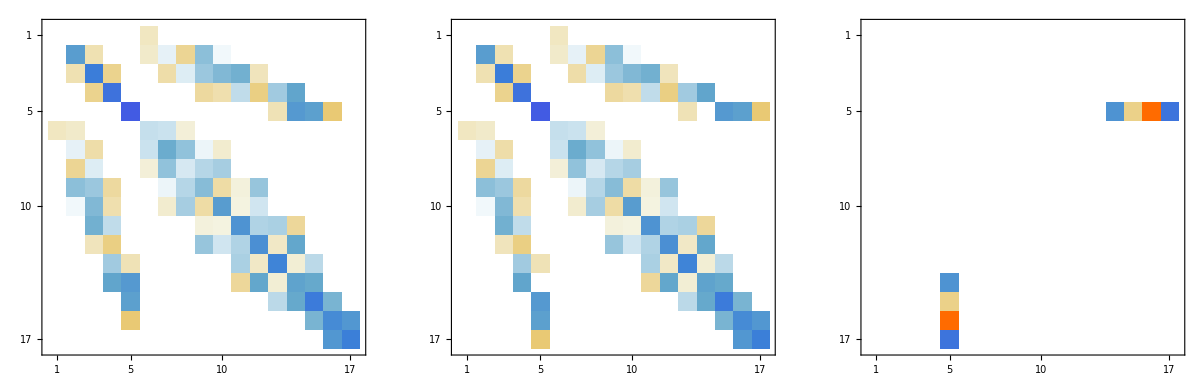
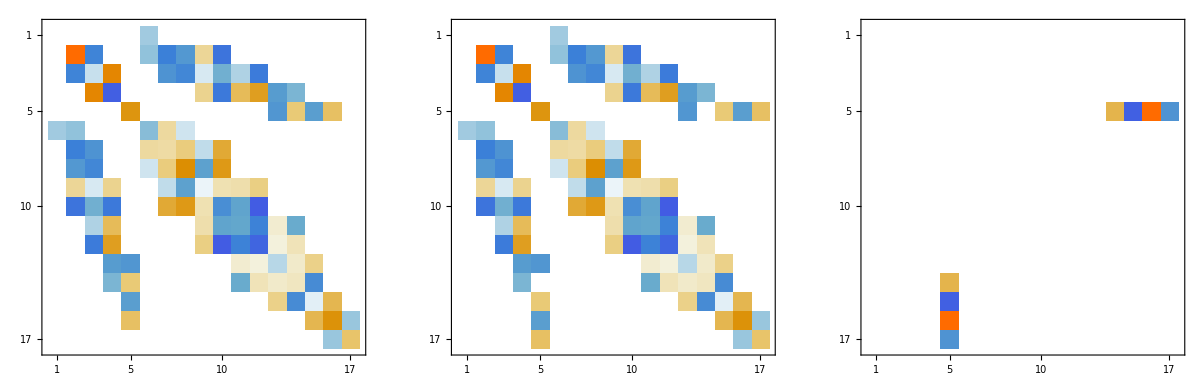
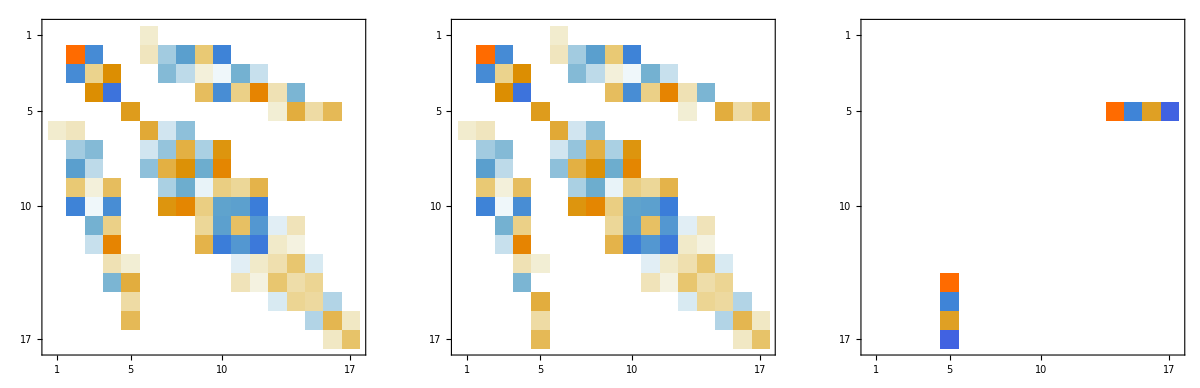
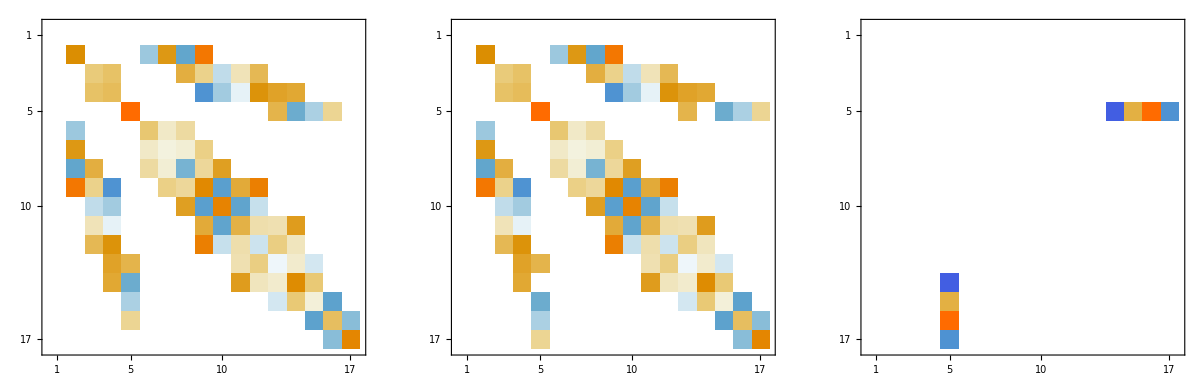
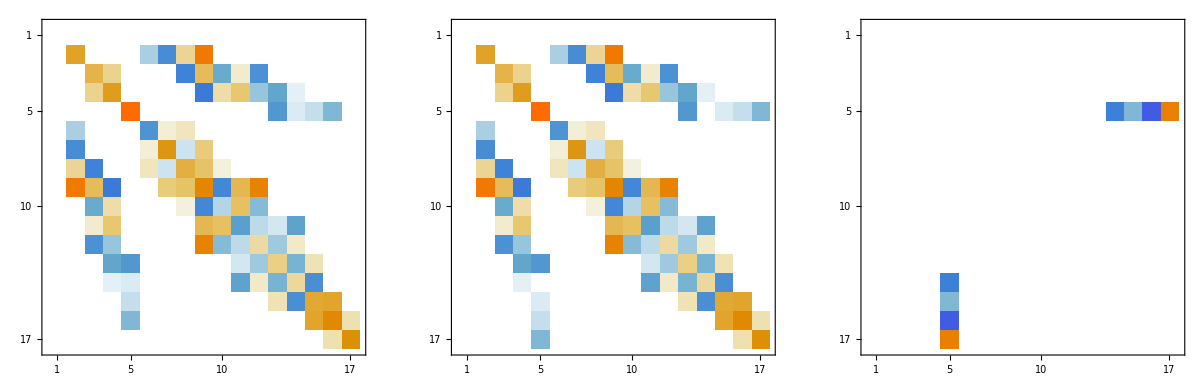
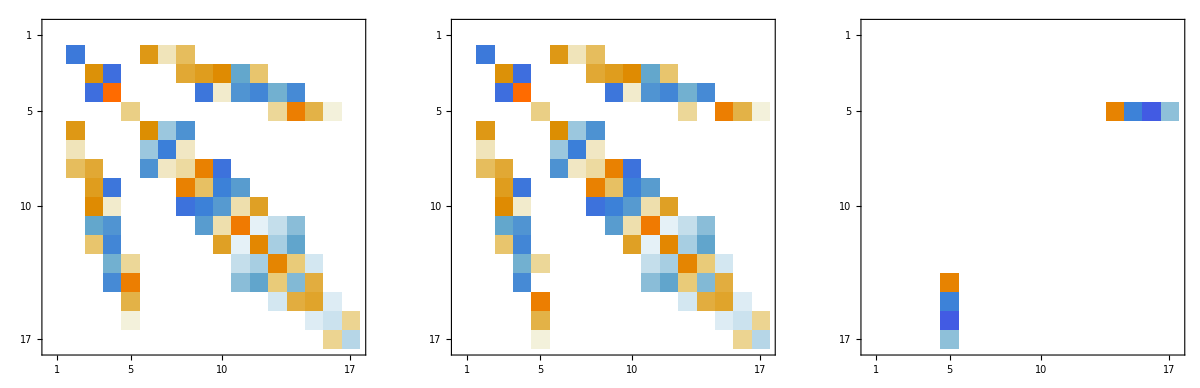
-Graphics-{M0,0.930102}
-Graphics-{M2,0.961892}
-Graphics-{M4,0.988961}
-Graphics-{P2,0.973619}
-Graphics-{P4,0.99575}
-Graphics-{P6,0.957749}

```mathematica
big=Column[rows]
```

```mathematica
Rasterize[big]
```

-Graphics-

```mathematica
plots=Table[(
PrintTemporary[numElectrons];
configTerms=fncross[["terms"]][numElectrons];
matrixReps=<||>;
Do[
(
magElements=fncross[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixReps[op]=tab
),
{op,MsAndPs}];
configTerms=fncrossDef[["terms"]][numElectrons];
matrixRepsDef=<||>;
Do[
(
magElements=fncrossDef[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixRepsDef[op]=tab
),
{op,MsAndPs}];

rows=Table[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
v1=Flatten[m1];
v2=Flatten[m2];
dist=(v1.v2)/(Sqrt[v1.v1] * Sqrt[v2.v2]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
{numElectrons,op,dist}
]
),{op,MsAndPs}];
Rasterize[Column[rows]]
)
,{numElectrons,{2,3,5,7}}];
```

```mathematica
Do[(
fname=FileNameJoin[{"~/Desktop","someplots","diff-f"<>{2,3,5,6}[[i]]<>".png"}];
Export[fname,plots[[i]]];
),{i,1,Length[plots]}]
```

## Crosswhite vs David

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qlanth.m"]
```

```mathematica
numElectrons=3;
allParams={E0,E1,E3,M0,M2,M4,P2,P4,P6,α,β,γ,ζ,B22,S22,B12,S12,B02,B44,S44,B34,S34,B24,S24,B14,S14,B04,B66,S66,B56,S56,B46,S46,B36,S36,B26,S26,B16,S16,B06,E2,T6,T7,T8,T11,T12,T14,T15,T16,T17,T18,T19,T2,T3,T4};
singleSymbol=α;
deletor=(#->0)&/@Select[allParams,Not[#===singleSymbol]&];
mat=HamMatrixAssembly[numElectrons,0];
mat=ReplaceInSparseArray[mat,deletor];
mat=ReplaceInSparseArray[mat,{singleSymbol->1}];
```

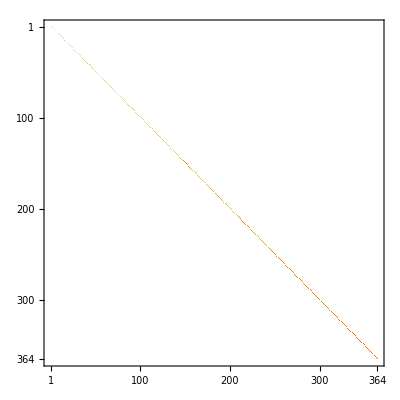

```mathematica
MatrixPlot[mat]
```

```mathematica
1/2 (-1+√(1+4#))&/@DeleteDuplicates[Sort[Eigenvalues[mat]]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
terms=StringSplit["4S 4D 4F 4G 4I 2P 2D1 2D2 2F1 2F2 2G1 2G2 2H1 2H2 2I 2K 2L"," "];
SLterms=findSL/@terms;
SLterms=SortBy[SLterms,Last];
```

```mathematica
rmat=Table[Tooltip[TwoBodyNKSL[bt,kt],{bt,kt}]/.{β->0,γ->0,α->α},{bt,terms},{kt,terms}];
rmat=Table[TwoBodyNKSL[bt,kt]/.{β->0,γ->0,α->1},{bt,terms},{kt,terms}];
```

```mathematica
1/2 (-1+√(1+4#))&/@Sort[DeleteDuplicates[Diagonal[rmat]]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
1/2 (-1+√(1+4#))&/@Sort[DeleteDuplicates[Diagonal[rmat]]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
1/2 (-1+√(1+4#))&/@DeleteDuplicates[Sort[Eigenvalues[rmat]]]
```

{0,1,1/2 (-1+√73),1/2 (-1+√145),7,1/2 (-1+√241),8,1/2 (-1+√337)}

```mathematica
findSL["2L"]
```

{1/2,8}

```mathematica
8*9
```

72

```mathematica
findSL["3P"]
```

{1,1}

```mathematica
Diagonal[mat]//Normal
```

{2,0,2,2,2,2,2,2,2,2,12,12,12,12,12,6,6,6,6,6,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,30,30,30,30,30,30,30,30,30,20,20,20,20,20,20,20,20,20,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,42,42,42,42,42,42,42,42,42,42,42,42,42}

```mathematica
Solve[y(y+1)==x,y]
```

{{y→1/2 (-1-√(1+4 x))},{y→1/2 (-1+√(1+4 x))}}

```mathematica
1/2 (-1+√(1+4#))&/@{0,2,6,12,20,30,42,56,72}
```

{0,1,2,3,4,5,6,7,8}

```mathematica
-1/2 (-1-√(1+4#))&/@{2,6,12,18,20,36,42,56,60,72}
```

{2,3,4,1/2 (1+√73),5,1/2 (1+√145),7,8,1/2 (1+√241),9}

```mathematica
Sort[DeleteDuplicates[Eigenvalues[mat]]]
```

{0,6,12,18,20,42,60,72,80,90,110,112,120,126,160,168,180,216,252}

```mathematica
Sort[DeleteDuplicates[Diagonal[Normal[mat]/.{α->1}]]]
```

{0,2,6,12,20,30,42,56,72}

```mathematica
Table[i*(i+1),{i,1,10,1}]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
ReplaceInSparseArray[mat,{}]
```

```mathematica
DeleteDuplicates[Flatten[Variables/@Flatten[Normal[mat]]]]
```

{E0,E1,E3,M0,M2,M4,P2,P4,P6,α,β,γ,ζ,B22,S22,B12,S12,B02,B44,S44,B34,S34,B24,S24,B14,S14,B04,B66,S66,B56,S56,B46,S46,B36,S36,B26,S26,B16,S16,B06,E2}

```mathematica
Flatten[mat]
```